```mathematica
(*
18.821 Project Laboratory in Mathematics
Author: Richard Chen
Created: 09/11/2024 2:39PM
Last Edited: 09/11/2024 2:40PM
*)
```

## Compute Chromatic Polynomials

```mathematica
completeBipartite[n_]:=Return[Graph[Range[2*n], Flatten[Outer[UndirectedEdge, Range[n],Range[n+1,2*n]]]]]
```

```mathematica
rootsChromatic[n_]:=Solve[ChromaticPolynomial[completeBipartite[n],q]==0,q]
```

```mathematica
N/@rootsChromatic[5]
```

{{q→0.},{q→1.},{q→2.00543},{q→2.68644},{q→2.95031-0.98416 ⅈ},{q→2.95031+0.98416 ⅈ},{q→3.23438-2.33208 ⅈ},{q→3.23438+2.33208 ⅈ},{q→3.46937-4.29118 ⅈ},{q→3.46937+4.29118 ⅈ}}

```mathematica
magnitude[x_]:=Sqrt[Re[x]^2 +Im[x]^2]
```

```mathematica
Abs[N[Flatten[Table[q/.rootsChromatic[n],{n,1,9}]]]]
```

{0.,1.,0.,1.,1.73205,1.73205,0.,1.,1.92339,1.92339,2.89477,2.89477,0.,1.,2.14886,2.14886,2.89447,2.89447,4.17709,4.17709,0.,1.,2.00543,2.68644,3.11013,3.11013,3.98746,3.98746,5.51822,5.51822,0.,1.,2.00015,2.92786,3.40634,3.40634,4.09463,4.09463,5.1587,5.1587,6.8964,6.8964,0.,1.,2.,2.9949,3.74314,3.74314,4.32028,4.32028,5.15519,5.15519,6.38446,6.38446,8.30062,8.30062,0.,1.,2.,2.99984,4.04554,4.04554,4.60431,4.60431,5.30439,5.30439,6.27491,6.27491,7.65058,7.65058,9.72433,9.72433,0.,1.,2.,3.,4.01086,4.54666,4.92086,4.92086,5.53392,5.53392,6.34643,6.34643,7.44099,7.44099,8.9479,8.9479,11.1633,11.1633}

## Plot Chromatic Polynomial Roots

```mathematica
(*With current method, time maxes out around n=10 for bipartite graph*)
```

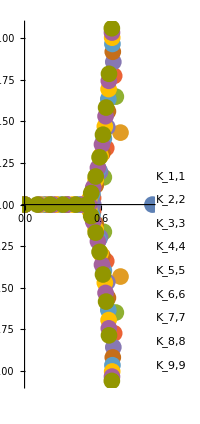

```mathematica
ComplexListPlot[Table[Labeled[Flatten[{q/n}/.rootsChromatic[n]],StringJoin[{"K_",ToString[n],",",ToString[n]}]],{n,1,10}],PlotStyle->PointSize[0.03]]
```

## Cuspidal curves

```mathematica
f[a_]:=a^1.5
```

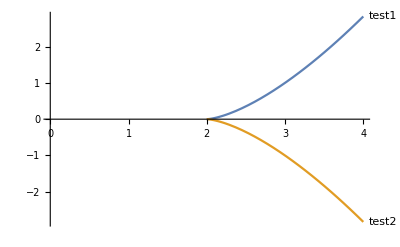

```mathematica
Plot[{Labeled[f[x-2],"test1"],Labeled[-f[x-2],"test2"]},{x,0,4}]
```

## Scratch Cells